This is a program written to find out what exactly happened when new perturbations of matter profiles are added.

# Prepare

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../../neuPackage/neutrino.wl"]
```

```mathematica
Get["../../neuPackage/neumat.wl"]
```

# New Combinations of n’s

## Parameters

```mathematica
gF=1.17*10^(-11)(*MeV^(-2)*)
ye=0.5
```

1.17×10^-11

0.5

```mathematica
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
omegaV=deltamsquare13/(2 energy10)(*MeV*);(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093/2]
```

0.153077

```mathematica
fraction=10
lambdaN=fraction*Cos[2thetaV]omegaV
```

10

1.23955×10^-15

```mathematica
Cos[2thetaV]-(lambdaN/omegaV)^2
```

-89.9627

```mathematica
thetamV=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi];
init={psi1[0],psi2[0]}=={1,0};
endpointN=1600;
```

List of Parameters for 1 2 3 frequiencies

```mathematica
onekList={0.999};
twokList={0.999,0.6};
oneaList={0.1};
twoaList={0.1,0.1};
onephiList={0};
twophiList={0,0};
threekList={0.999,0.6,0.4};
threeaList={0.1,0.1,0.1};
threephiList={0,0,0};
thetaVRes=thetaV;
thetamVRes=thetamV;
omegaVRes=omegaV;
endpointNRes=endpointN*15/20
```

1200

## Superposition

```mathematica
oneListFullTicks=Table[{x,ScientificForm[MeVInverse2km[x/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]],2]},{x,0,endpointNRes}];
```

```mathematica
oneListTicks=Take[oneListFullTicks,{1,Length@oneListFullTicks,Floor[(Length@oneListFullTicks)/5]}];
```

```mathematica
oneListTicks
```

{{0,0.},{240,4.×10^3},{480,8.1×10^3},{720,1.2×10^4},{960,1.6×10^4},{1200,2.×10^4}}

```mathematica
oneNPlt=pltNum[onekList,oneaList,onephiList,thetamVRes,endpointNRes,"Single Frequency",{Red,Dashed},oneListTicks,"Distance (km)"];
```

```mathematica
oneListPlt=pltNList[{{1}},onekList,oneaList,onephiList,thetamVRes,endpointNRes,"Single Frequency",Blue,oneListTicks,"Distance (km)"];
```

```mathematica
twoNPlt=pltNum[twokList,twoaList,twophiList,thetamVRes,endpointNRes,"Two Frequencies",{Red,Dashed},oneListTicks,"Distance (km)"];
```

```mathematica
twoEffectiveList=Flatten[ Drop[Part[qValueOrderdList[listNGenerator[2,4],twokList,twoaList,twophiList,thetamVRes],1;;2],None,{2}],1]
```

{{1,0},{0,1}}

```mathematica
twoListPlt=pltNList[twoEffectiveList,twokList,twoaList,twophiList,thetamVRes,endpointNRes,"Approximation;",Blue,oneListTicks,"Distance (km)"];
```

```mathematica
threeNPlt=pltNum[threekList,threeaList,threephiList,thetamVRes,endpointNRes,"Three Frequencies Numerical",{Red,Dashed},oneListTicks,"Distance (km)"];
```

```mathematica
threeEffectiveList=Flatten[ Drop[Part[qValueOrderdList[listNGenerator[3,4],threekList,threeaList,threephiList,thetamVRes],1;;4],None,{2}],1]
```

{{0,-1,4},{0,1,1},{0,3,-2},{1,0,0}}

```mathematica
threeListPlt=pltNList[{threeEffectiveList[[2]],threeEffectiveList[[4]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"Approximation;",Blue,oneListTicks,"Distance (km)"];
```

```mathematica
(*Grid[{{Show[oneListPlt,oneNPlt]},{Show[twoListPlt,twoNPlt]},{Show[threeListPlt,threeNPlt]}}]*)
```

### Can we just linearly add up all the oscillations from each combinations of n’s?

For two frequency case, we have the useful combination to be

```mathematica
twoEffectiveList
```

{{1,0},{0,1}}

Now we grab the each one and make lists of transition probabilities

```mathematica
phi2ListDataNList[listInput_,kNList_,aNList_,phiNList_,thetam_,endpoint_,step_:1,startpoint_:0]:=Table[Evaluate[neumat`Private`psi2[x]/.First@solNList[listInput,kNList,aNList,phiNList,thetam,endpoint]],{x,startpoint,endpoint,step}];
(*MapThread[{#1,#2}&,
{Table[x,{x,startpoint,endpoint,step}],
Table[Evaluate[Abs[psi2[x]]^2/.First@solNList[listInput,aNList,kNList,phiNList,thetam,endpoint]],{x,startpoint,endpoint,step}]}
]*)
```

```mathematica
twoListDatax=Table[x,{x,0,endpointNRes,100}];
twoListData1=phi2ListDataNList[{twoEffectiveList[[1]]},twoaList,twokList,twophiList,thetamVRes,endpointNRes,100];
twoListData2=phi2ListDataNList[{twoEffectiveList[[2]]},twokList,twoaList,twophiList,thetamVRes,endpointNRes,100];
```

```mathematica
listPltNList[listData_,legends_,color_,frameTicks_,frameLabel_]:=ListPlot[listData,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x",frameLabel}},PlotStyle->color,PlotLegends->Placed[Style[ToString[legends],color],{Top,Center}],FrameTicks->{{Automatic,None},{Automatic,frameTicks}}]
```

Show the plots for each n list

```mathematica
(*twoListData1Plt=listPltNList[MapThread[{#1,Abs[#2]^2}&,{twoListDatax,twoListData1}],"List 1;",Magenta,oneListTicks,"Distance (km)"]
twoListData2Plt=listPltNList[MapThread[{#1,Abs[#2]^2}&,{twoListDatax,twoListData2}],"List 2;",Magenta,oneListTicks,"Distance (km)"]*)
```

```mathematica
(*Show[twoListData1Plt,twoNPlt,PlotRange->All]*)
```

Two frequencies doens’t really help us. Should check three frequencies.

```mathematica
threeEffectiveList
```

{{0,-1,4},{0,1,1},{0,3,-2},{1,0,0}}

```mathematica
threeListDatax=Table[x,{x,0,endpointNRes,100}];
threeListDataFull=Table[
phi2ListDataNList[{threeEffectiveList[[i]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100]
,{i,1,Length@threeEffectiveList}];
threeListData1=phi2ListDataNList[{threeEffectiveList[[1]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100];
threeListData2=phi2ListDataNList[{threeEffectiveList[[2]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100];
threeListData3=phi2ListDataNList[{threeEffectiveList[[3]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100];
threeListData4=phi2ListDataNList[{threeEffectiveList[[4]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100];
```

```mathematica
threeListData=Total@threeListDataFull;
threeListDataTemp=threeListData2+threeListData4;
```

Show the plots together

```mathematica
(*Show[listPltNList[MapThread[{#1,Abs[#2]^2}&,{threeListDatax,threeListData}],"Linear Superposition;",Magenta,oneListTicks,"Distance (km)"],threeListPlt,threeNPlt]*)
```

Show the q values

```mathematica
(*qValueOrderdList[listNGenerator[3,4],threekList,threeaList,threephiList,thetamVRes];*)
```

A show the plots of each list

```mathematica
(*pltNList[{threeEffectiveList[[1]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"Approximation;",Blue,oneListTicks,"Distance (km)"]
pltNList[{threeEffectiveList[[4]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"List 4;",Blue,oneListTicks,"Distance (km)"]
pltNList[{threeEffectiveList[[2]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"List 2;",Blue,oneListTicks,"Distance (km)"]
pltNList[{threeEffectiveList[[3]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"List 3;",Blue,oneListTicks,"Distance (km)"]*)
```

```mathematica
Table[widthNList[threeEffectiveList[[i]],threekList,threeaList,threephiList,thetamVRes],{i,1,4}]
```

{1.40709×10^-9,0.0000172096,1.25031×10^-9,0.0000817769}

## Destruction of Resonance

First of all we have to have an idea of the range of the solution (in unit of km)

```mathematica
ScientificForm[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]],2]
Chop[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]]
```

2.×10^4

20213.5

```mathematica
Table[Evaluate[Abs[neumat`Private`psi2[x]]^2/.First@solNum[twokList,twoaList,twophiList,thetamVRes,endpointNRes]],{x,0,2000,100}
]
```

InterpolatingFunction::dmval: Input value {1300} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1400} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1500} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{0.,0.0000732758,0.000273108,0.000623854,0.00110007,0.00167252,0.00244051,0.00325211,0.00418112,0.00524575,0.00632837,0.00752115,0.0088401,7913.3,504822.,5.74154×10^6,3.22336×10^7,1.229×10^8,3.66855×10^8,9.24849×10^8,2.06036×10^9}

```mathematica
probTransitListData[kNList_,aNList_,phiNList_,thetam_,endpoint_,step_:1,startpoint_:0]:=Module[
{thetaVResM,thetamVResM,omegaVResM,endpointNResM,twokListM,twoaListM,twophiListM},

twokListM=kNList;
twoaListM=aNList;
twophiListM=phiNList;
thetaVResM=thetaV;
thetamVResM=thetam;
omegaVResM=omegaV;
endpointNResM=endpoint;(*1600*15*)

Table[Evaluate[Abs[neumat`Private`psi2[x]]^2/.First@solNum[kNList,aNList,phiNList,thetam,endpoint]],{x,startpoint,endpoint,step}]
]
```

Now obtain amplitude of the transitions as a function of k2

```mathematica
k1MaxAmpListDatak1={0.1,2,0.01};
k1MaxAmpListDatax=Table[k1,{k1,k1MaxAmpListDatak1[[1]],k1MaxAmpListDatak1[[2]],k1MaxAmpListDatak1[[3]]}];
k1MaxAmpListData=Table[Max[probTransitListData[{k1},oneaList,onephiList,thetamVRes,endpointNRes,10,0]],{k1,k1MaxAmpListDatak1[[1]],k1MaxAmpListDatak1[[2]],k1MaxAmpListDatak1[[3]]}]
k1MaxAmpListDataFullTicks=Table[{k1,ScientificForm[MeVInverse2km[2Pi/(k1*OmegaMatter[thetamVRes,thetaVRes,omegaVRes])],2]},{k1,k1MaxAmpListDatak1[[1]],k1MaxAmpListDatak1[[2]],k1MaxAmpListDatak1[[3]]}];
k1MaxAmpListDataTicks=Take[k1MaxAmpListDataFullTicks,{1,Length@k1MaxAmpListDataFullTicks,Floor[(Length@k1MaxAmpListDataFullTicks)/5]}];
```

{3.86114×10^-8,4.16686×10^-8,4.36451×10^-8,4.51055×10^-8,4.61948×10^-8,4.57866×10^-8,4.68804×10^-8,4.91813×10^-8,4.69742×10^-8,4.9874×10^-8,4.12829×10^-8,3.99075×10^-8,5.64631×10^-8,5.84125×10^-8,5.95808×10^-8,6.09753×10^-8,6.17134×10^-8,6.46134×10^-8,6.45551×10^-8,6.93609×10^-8,6.90728×10^-8,7.50894×10^-8,7.86643×10^-8,1.22934×10^-7,8.59187×10^-8,8.54076×10^-8,8.86042×10^-8,5.37343×10^-8,9.1824×10^-8,1.05831×10^-7,9.39434×10^-8,1.11942×10^-7,1.11016×10^-7,1.40999×10^-7,1.53277×10^-7,1.79402×10^-7,2.0219×10^-7,2.77096×10^-7,4.4273×10^-7,1.13874×10^-6,0.0001049,1.09672×10^-6,4.33627×10^-7,2.84776×10^-7,2.41905×10^-7,2.22659×10^-7,2.05107×10^-7,2.03981×10^-7,2.03586×10^-7,1.90461×10^-7,2.08698×10^-7,2.11724×10^-7,2.23407×10^-7,1.79992×10^-7,2.40806×10^-7,2.42101×10^-7,2.48661×10^-7,2.76178×10^-7,2.83072×10^-7,2.87649×10^-7,3.29437×10^-7,3.3557×10^-7,3.72156×10^-7,3.97004×10^-7,4.03474×10^-7,4.36826×10^-7,4.80939×10^-7,4.91972×10^-7,5.91385×10^-7,6.14473×10^-7,6.78039×10^-7,7.7312×10^-7,8.79085×10^-7,9.69767×10^-7,1.10465×10^-6,1.26132×10^-6,1.40579×10^-6,1.66983×10^-6,1.89845×10^-6,2.32306×10^-6,2.79971×10^-6,3.40683×10^-6,4.32677×10^-6,5.70943×10^-6,7.79899×10^-6,0.0000112087,0.0000174067,0.0000309793,0.0000697046,0.000279131,0.0100438,0.00028195,0.0000712607,0.0000319883,0.000018153,0.0000117314,8.16992×10^-6,5.98337×10^-6,4.67133×10^-6,3.7355×10^-6,3.07025×10^-6,2.56096×10^-6,2.15774×10^-6,1.85025×10^-6,1.58948×10^-6,1.41708×10^-6,1.25813×10^-6,1.12166×10^-6,1.01225×10^-6,9.11292×10^-7,8.32902×10^-7,7.32752×10^-7,6.7171×10^-7,6.06411×10^-7,5.94427×10^-7,5.52101×10^-7,5.14347×10^-7,4.80238×10^-7,4.44872×10^-7,4.17432×10^-7,3.96696×10^-7,3.68548×10^-7,3.53312×10^-7,3.34814×10^-7,3.16921×10^-7,2.98055×10^-7,2.81428×10^-7,2.72095×10^-7,2.43779×10^-7,2.48429×10^-7,2.26438×10^-7,2.27727×10^-7,2.17305×10^-7,2.0712×10^-7,1.98207×10^-7,1.93279×10^-7,1.82097×10^-7,1.77731×10^-7,1.68998×10^-7,1.65392×10^-7,1.6143×10^-7,1.55852×10^-7,1.46193×10^-7,1.43381×10^-7,1.4023×10^-7,1.36286×10^-7,1.31771×10^-7,1.2755×10^-7,1.23376×10^-7,8.31686×10^-8,1.17779×10^-7,1.14352×10^-7,1.10988×10^-7,7.75023×10^-8,1.04524×10^-7,1.00454×10^-7,9.94431×10^-8,9.731×10^-8,9.41316×10^-8,9.18029×10^-8,9.00552×10^-8,8.78286×10^-8,8.63028×10^-8,8.44014×10^-8,8.2303×10^-8,8.00947×10^-8,7.88874×10^-8,7.71799×10^-8,7.50409×10^-8,7.36698×10^-8,6.81678×10^-8,7.06605×10^-8,6.84402×10^-8,6.78098×10^-8,6.65661×10^-8,6.48242×10^-8,6.25264×10^-8,6.20841×10^-8,5.98566×10^-8,5.94874×10^-8,5.88349×10^-8,5.69328×10^-8,5.66041×10^-8,5.58258×10^-8,5.48445×10^-8,5.34919×10^-8,5.30368×10^-8,4.9231×10^-8,5.11928×10^-8,4.98284×10^-8,4.97149×10^-8}

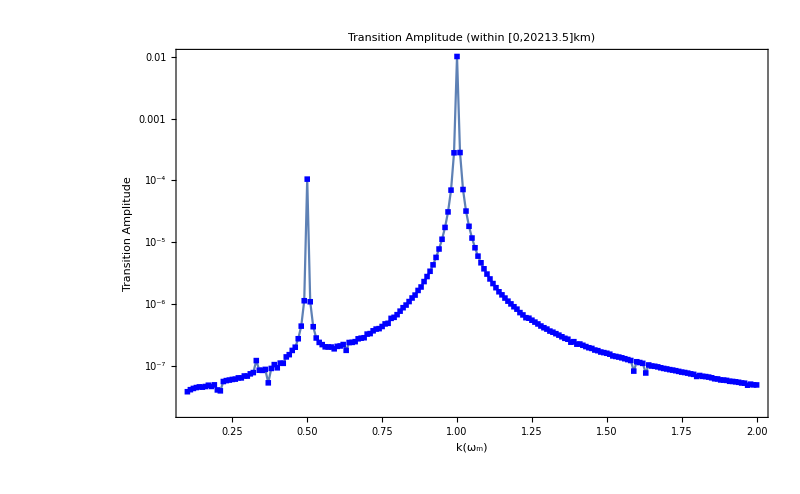

```mathematica
k1MaxAmpListDataListLogPlot=ListLogPlot[MapThread[{#1,#2}&,{k1MaxAmpListDatax,k1MaxAmpListData}],Joined->True,PlotMarkers->Style["■", Small, Blue],Frame->True,ImageSize->imgsize,PlotLabel->"Transition Amplitude (within [0,"<>ToString[Chop[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]]]<>"]km)",FrameLabel->{{"Transition Amplitude",None},{"k(ω_m)","Fluction Wavelength (km)"}},FrameTicks->{{Automatic,None},{Automatic,k1MaxAmpListDataTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18},ImagePadding->{{Automatic,Automatic},{Automatic,60}},PlotRange->Full]
```

For Two frequencies

```mathematica
k2MaxAmpListDatak1=1;
k2MaxAmpListDatak2={0.1,1.1,0.01};
k2MaxAmpListDatax=Table[k2,{k2,k2MaxAmpListDatak2[[1]],k2MaxAmpListDatak2[[2]],k2MaxAmpListDatak2[[3]]}];
```

```mathematica
k2MaxAmpListData=Table[Max[probTransitListData[{k2MaxAmpListDatak1,k2},twoaList,twophiList,thetamVRes,endpointNRes,10,0]],{k2,k2MaxAmpListDatak2[[1]],k2MaxAmpListDatak2[[2]],k2MaxAmpListDatak2[[3]]}]
k2MaxAmpListDataFullTicks=Table[{k2,ScientificForm[MeVInverse2km[2Pi/(k2*OmegaMatter[thetamVRes,thetaVRes,omegaVRes])],2]},{k2,k2MaxAmpListDatak2[[1]],k2MaxAmpListDatak2[[2]],k2MaxAmpListDatak2[[3]]}];
k2MaxAmpListDataTicks=Take[k2MaxAmpListDataFullTicks,{1,Length@k2MaxAmpListDataFullTicks,Floor[(Length@k2MaxAmpListDataFullTicks)/5]}];
```

{0.00586531,0.00649491,0.00700871,0.00742531,0.00776,0.00803134,0.00825632,0.00844178,0.00858767,0.00870525,0.00882073,0.00893368,0.00904465,0.00914447,0.00923164,0.00930241,0.0093574,0.0094012,0.0094336,0.00945278,0.00946614,0.0094917,0.00953904,0.00959472,0.00963866,0.00966757,0.0096914,0.00971407,0.0097287,0.00972863,0.00971659,0.00970432,0.0097075,0.00973429,0.00977567,0.00980916,0.00981858,0.00980985,0.00980506,0.00982136,0.00995849,0.0098848,0.00989227,0.00987797,0.00986227,0.00986785,0.00989917,0.00993983,0.00996677,0.00996802,0.00994821,0.00992126,0.00989877,0.00988491,0.00988024,0.00988726,0.00990923,0.0099446,0.00998313,0.0100101,0.0100146,0.009996,0.0099633,0.00992766,0.00990022,0.00988813,0.00989619,0.00992616,0.00997265,0.0100229,0.0100597,0.0100689,0.0100462,0.00999779,0.00993846,0.00988571,0.00985631,0.0098627,0.00990975,0.00999113,0.0100868,0.0101682,0.0102051,0.0101751,0.0100701,0.00989951,0.00968267,0.00945616,0.00925727,0.00912208,0.0394766,0.00913281,0.00927597,0.009478,0.00970332,0.00991385,0.0100783,0.0101766,0.0102035,0.0101693,0.0100963}

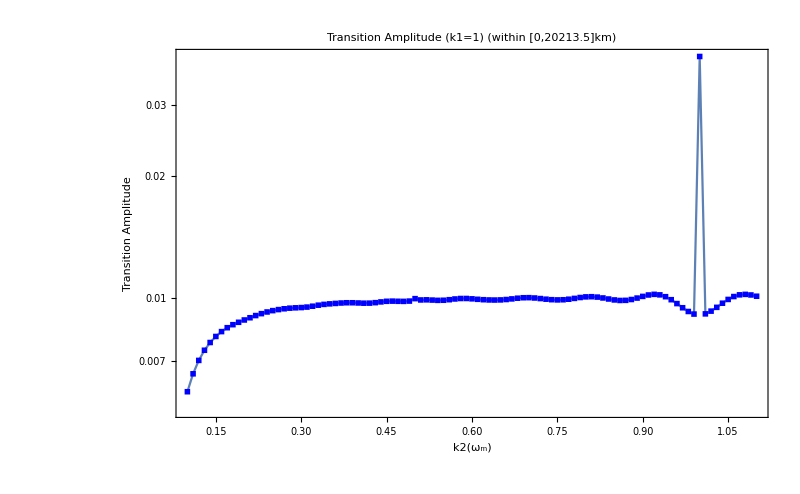

```mathematica
k2MaxAmpListDataListLogPlot=ListLogPlot[MapThread[{#1,#2}&,{k2MaxAmpListDatax,k2MaxAmpListData}],Joined->True,PlotMarkers->Style["■", Small, Blue],Frame->True,ImageSize->imgsize,PlotLabel->"Transition Amplitude (k1="<>ToString[k2MaxAmpListDatak1]<>") (within [0,"<>ToString[Chop[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]]]<>"]km)",FrameLabel->{{"Transition Amplitude",None},{"k2(ω_m)","Fluction Wavelength (km)"}},FrameTicks->{{Automatic,None},{Automatic,k1MaxAmpListDataTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18},ImagePadding->{{Automatic,Automatic},{Automatic,60}},PlotRange->Full]
```

Make Plots of some of the k’s

```mathematica
pltNum[{0.5},oneaList,onephiList,thetamVRes,endpointNRes*10,"Only 1",Blue,None,None]
```

-Graphics-

```mathematica
Manipulate[pltNum[{0.5,k2},{0.1,a2},twophiList,thetamVRes,endpointNRes*10,ToString[k2],Blue,None,None],{{k2,0.8},0.0001,1,0.0001},{{a2,0.1},0.001,0.2}]
```

```mathematica
Table[pltNum[{0.999,k2},{0.1,0.05},twophiList,thetamVRes,endpointNRes,"A1=A2=0.1; k1=0.999,"<>"k2="<>ToString[k2],Blue,None,None],{k2,0.9,1,0.1}]
```

{-Graphics-,-Graphics-}

```mathematica
Table[pltNum[{0.999,k2},twoaList,twophiList,thetamVRes,endpointNRes,ToString[k2],Blue,None,None],{k2,0.0001,1,0.2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}